## Code

```mathematica
(* f is a function taking a polygon *)
colorValues[data_,f_]:=
Module[{zz,zzz,zzzz},
zz=rfCoords[
data,
CoordIndex1->-2,
CoordsOnly->True,
OutputInRad->True];
zzz=Map[Partition[#,2]&,zz];
zzzz=Map[f,zzz];
Return[zzzz]
]
```

## Use

```mathematica
<<Topy/vizhandmap2.m
```

```mathematica
<<Topy/polygongeometry.m
```

```mathematica
data=Import["/Users/research2/projects/2013-topy/mk9RFS-edited.txt",
"Table"];
```

```mathematica
cf=ColorData["DarkRainbow"];
```

### random color

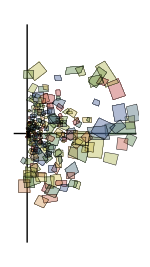

```mathematica
vizHandmap1[
data,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150,
PolygonColorFunc->Function[{x},cf[Random[]]],
PolygonStyleFunc->Function[{x},
{EdgeForm[{Black,Thickness[0.002]}],
FaceForm[Opacity[0.4]]}]
]
```

### Coloring by eccentricity

```mathematica
ecc=colorValues[data,polygonEccentricity];
```

```mathematica
colors=Map[cf,(ecc-Min[ecc])/(Max[ecc]-Min[ecc])];
```

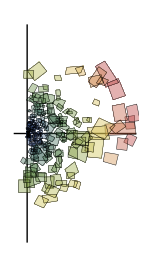

```mathematica
vizHandmap1[
data,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150,
PolygonColorFunc->colors,
PolygonStyleFunc->Function[{x},
{EdgeForm[{Black,Thickness[0.002]}],
FaceForm[Opacity[0.4]]}]
]
```

### Coloring by RF area

```mathematica
ecc=colorValues[data,polygonArea];
```

```mathematica
colors=Map[cf,(ecc-Min[ecc])/(Max[ecc]-Min[ecc])];
```

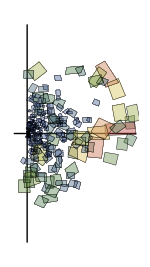

```mathematica
vizHandmap1[
data,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150,
PolygonColorFunc->colors,
PolygonStyleFunc->Function[{x},
{EdgeForm[{Black,Thickness[0.002]}],
FaceForm[Opacity[0.4]]}]
]
```

### Coloring according to penetration

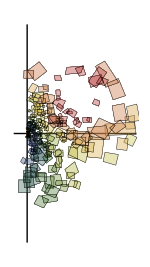

```mathematica
vizHandmap2[
data,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150,
TractColorFunc->cf,
PolygonStyleFunc->Function[{x},
{EdgeForm[{Black,Thickness[0.002]}],
FaceForm[Opacity[0.4]]}]
]
```

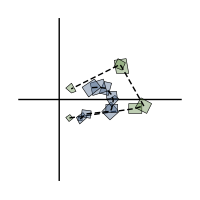

```mathematica
vizHandmap2[
data,
CoordIndex1->-2,
LongitudeRange->{-5Degree,15Degree},
LatitudeRange->{-10Degree,10Degree},
Resolution->5 Degree,
ImageSize->200,
TractColorFunc->cf,
PolygonStyleFunc->Function[{x},
{EdgeForm[{Black,Thickness[0.002]}],
FaceForm[Opacity[0.4]]}],
DisplayTracts->{50,64},
PolygonCenterConnectorStyle->Directive[{Thickness[0.005],Dashing[{0.02,0.01}]}]
]
```